## An Abstract Model of Historical Processes - Code

## Context

This Mathematica notebook implements a sociological model of power struggles described in my (draft) paper An Abstract Model of Historical Processes.  For more information, please see the paper itself, which can be found at: https://papers.ssrn.com/sol3/papers.cfm?abstract_id=2818471.

Author: Michael Poulshock, Drexel University Thomas R. Kline School of Law, mp988@drexel.edu, mpoulshock@gmail.com.

## Implementation

### Data Structures

#### Tactic matrix

An example of a tactic matrix (representing all of the agents’ tactic vectors), displayed in matrix form.  Each agent is allocating half of its power to itself, as indicated by the main diagonal.  Note that the absolute values of the cells in each column sum to one.

```mathematica
{{0.5,0.3},{-0.5,0.7}}// MatrixForm
```

(0.5 | 0.3
-0.5 | 0.7)

The tactic matrix is composed of each agent’s tactic vector:

```mathematica
Transpose[{{0.5,0.3},{-0.5,0.7}}][[1]]
```

{0.5,-0.5}

The absolute value of a tactic vector must always sum to one:

```mathematica
Total[Abs[%]]
```

1.

#### Game state

The game state is represented as an association that includes agent sizes, a tactic matrix, a utility vector, and a distance vector.

```mathematica
<|"sizes"->{4.3,4.2},"tactics"->{{0.5,0.5},{-0.5,0.5}},"util"->{2.2,2.1},"dx"->0.1|>
```

#### Options

The meaning and ranges of the parameters are as follows (see the paper for details):

n | Number of players | ∈[1,∞) | Int
α | Utility exponent | ∈[2,3] | Real
β | Benevolence multiplier | ∈(0,μ) | Real
μ | Malevolence multiplier | ∈(β,∞) | Real
δ | Discounting factor | ∈(0,1) | Real
σ | Coefficient of inertia | ∈(0,n] | Real
breadth | Tactics per player | ∈[1,∞) | Int
depth | Tactics/player in search for Nash equilibria | ∈[1,∞) | Int
probes | No. of searches for intertemporal equilibria | ∈[1,∞) | Int
nearness | Tactical variation in simulation | ∈(0,1] | Real

They are set as global variables:

```mathematica
(* Model Parameters *)
n=3;
α=2.5;
β=2;
μ=3;
δ=0.8;
σ=0.1;

(* Simulation Parameters *)
breadth=4;
depth=15;
probes = 2;
nearness=1;  (* higher = more variation *)

(* Derived Data Structures *)
discountVector = Table[δ^i,{i,0,depth-1}];
```

#### Reel

A reel is a list of game states that can be played frame-by-frame to illustrate the evolution of a system of interacting, power-seeking agents.

```mathematica
{state0, state1, ...}
```

### Game State

#### Nearby tactics

Given a random vector, this function adjusts its length so as to make it a legal tactic.  A legal tactic is a point on the surface of a cross-polytope whose dimension is equal to the number of agents.  The visualization below illustrates this shape for a population of three agents.  We assume that agents do not harm themselves.

```mathematica
normalize[vector_] := N[vector / Total[Abs[vector]]]
```

Try using Round to improve performance?

```mathematica
normalize[vector_] :=Round[vector / Total[Abs[vector]],0.001]
```

```mathematica
normalize[{3,22,1,-4}]
```

{0.1,0.733333,0.0333333,-0.133333}

Finds tactics “near” a given tactic.  Method: Add random variates to each element of the input tactic, then normalize the vector so it is on the surface of the cross polytope.  If the vector contains negative tactic for a given agent (indicating self-harm), ignore the result and look for a new nearby random tactic.

```mathematica
randomTacticNear[point_, agentIndex_] := Block[{newRaw},
newRaw = point + RandomVariate[NormalDistribution[0,nearness],Length[point]];
newRaw[[agentIndex]]=Abs[newRaw[[agentIndex]]];
Return[normalize[newRaw]];
]
```

Same as above, but it generates a list of nearby tactics:

```mathematica
randomTacticsNear[point_, a_,numberOfTactics_] := Table[randomTacticNear[point, a],numberOfTactics]
```

```mathematica
randomTacticNear[{1,0,0}, 1]
```

{0.999895,-0.0000125441,0.0000924997}

```mathematica
randomTacticsNear[{1,0,0}, 1,5 ] // Column
```

{0.999893,0.0000396606,-0.0000676619}
{0.999998,6.45049×10^-7,1.39843×10^-6}
{0.999934,0.000044192,0.0000220727}
{0.999671,0.0000966989,-0.000232239}
{0.999986,5.70123×10^-6,8.32925×10^-6}

A cross-polytope in dimension 3 is an octahedron, shown below.  Legal tactics are points on the surface of this shape.  The widget below starts from a given point (pt) and then generates random points nearby, where the slider controls the degree of nearness.

```mathematica
Manipulate[
pt = {0.7,0.1,0.2};
nearness=near;
Show[{
Graphics3D[Scale[PolyhedronData["Octahedron","Faces"],1.4,{0,0,0}]],
Graphics3D[{PointSize[0.02],Point[pt]}],
Graphics3D[Point[randomTacticsNear[pt,3,100] ], PlotRange->{{-1,1},{-1,1},{-1,1}}]
}],{near,0.0001,1}]
```

#### Nearby matrices

This function takes a tactic matrix and returns a random “nearby” matrix in which every agent’s tactic is near their old one.

```mathematica
randomMatrixNear[m_] := Transpose[Table[randomTacticNear[m[[All,a]], a],{a,1,n}]]
```

```mathematica
randomMatrixNear[{{0.5,0.5,0},{0.5,0.5,-0.1},{0,0,0.9}}]
```

{{0.49985,0.493347,-0.00105989},{0.491966,0.492171,-0.0948707},{0.00818425,-0.0144812,0.904069}}

For each agent, generate a list of random tactics.  Then, given those tactics, generate an ensemble of random tactic matrices, representing all combinations of all agents’ tactics.  The total number of matrices created is breadth^n.  For performance reasons, this function does not use randomMatrixNear.

```mathematica
matrixPermutations[m_] := Map[Transpose,Tuples[Table[randomTacticsNear[m[[All,a]], a,breadth],{a,1,n}]]]
```

```mathematica
matrixPermutations[{{0.5,0.5,0},{0.5,0.5,-0.1},{0,0,0.9}}]
```

From a given tactic matrix, generate a sequence of random matrices in which each one is “near” the prior one.

```mathematica
randomMatrixSequence[m_] := Rest[NestList[randomMatrixNear,m,depth]]
```

```mathematica
randomMatrixSequence[IdentityMatrix[3]]
```

#### New game state

Creates a new game state object:

```mathematica
newState[sizes_,tactics_]:= 
 <|"sizes"->sizes,
"tactics"->tactics,
"util"->utility[sizes],
"dx"->0 |>
```

```mathematica
newState[{1,1,1},{{0.5,0.5,0},{0.5,0.5,-0.1},{0,0,0.9}}]
```

<|sizes→{1,1,1},tactics→{{0.5,0.5,0},{0.5,0.5,-0.1},{0,0,0.9}},util→{0.333333,0.333333,0.333333},dx→0|>

#### Random game states

Generate a random initial game state, specifying the number of nodes (n), the maximum node size, and the degree of nearness from the identity matrix:

```mathematica
randomGameState:= newState[RandomReal[{0,1},n],randomMatrixNear[IdentityMatrix[n]]]
```

```mathematica
randomGameState
```

<|sizes→{0.868015,0.122082,0.719793},tactics→{{0.669004,-0.211752,-0.251489},{0.257059,0.47977,-0.137554},{-0.0739362,-0.308478,0.610957}},util→{0.545661,0.00404797,0.341684},dx→0|>

#### Update game state

At every time step, we update the state of the nodes (which may grow or shrink) to get a new game state.  Procedure used: (1) multiply the tactics by the benevolence and malevolence constants, (2) use matrix multiplication to obtain the new node sizes.

```mathematica
updateState[parentState_,newTactics_]:= Block[{skewedTactics,newNodes,newUtil,dx},

(* Apply the benevolence & malevolence constants to the tactic matrix *)
skewedTactics = tacticSkew[newTactics]; 

(* Use the dot product to get the new node sizes. Ensure that the result does not produce nodes with negative sizes. *)
newNodes = Map[Max[#,0]&, Dot[skewedTactics,parentState["sizes"]]];

(* Calculate the "tactical distance" from the parent tactic matrix to the child matrix. *)
dx = tacticalDistance[parentState["tactics"],newTactics];

newUtil =utility[newNodes];

Return[<|
"sizes" ->newNodes,
"tactics" -> newTactics,
"util"->newUtil,
"dx"->dx
|>]
]
```

Some tests of the function above:

```mathematica
updateState[randomGameState,randomMatrixNear[IdentityMatrix[n]]]
```

<|sizes→{0.32142,0.508853,0.566817},tactics→{{0.905983,0.112522,-0.0363275},{-0.0672667,0.805619,0.203649},{0.0267499,-0.0818594,0.760024}},util→{0.0856898,0.270226,0.353878},dx→0.377128|>

Before doing the matrix multiplication, we multiply the cells in the tactic matrix by either a malevolence factor (if the tactic is negative) or a benevolence factor (if it’s positive).  Any transfers of power from a node back to itself are not subject to this multiplication.

```mathematica
tacticSkew[tactics_] := Block[{newTactics,i},

(* Increase all transfers to other nodes by the appropriate factor *)
 newTactics = Map[applySkew[#,μ,β]&,tactics, {2}];

(* Undo the increases for self-transfers (along the matrix diagonal) *)
For[i=1,i≤n,i++,  
newTactics[[i,i]] = tactics[[i,i]];
]; 

Return[newTactics];
];
```

```mathematica
applySkew=Compile[{{val,_Real},{conflict, _Real},{coop, _Real}},If[val<0, val*conflict, val*coop]];
```

```mathematica
tacticSkew[{{0.5,0.5,0},{0.5,0.5,-0.1},{0,0,0.9}}] // AbsoluteTiming
```

{0.000065,{{0.5,0.55,0.},{0.55,0.5,-0.3},{0.,0.,0.9}}}

#### Play out a sequence of tactic matrices

Given a sequence of tactic matrices and an initial state, play out the sequence of moves and determine the results at each step.  This is a “line of play.”

```mathematica
playTacticMatrixSequence[initialState_, tacticMatrixSequence_] := FoldList[updateState,initialState,tacticMatrixSequence]
```

### Utility / Payoff

#### Utility function

This function determines the “utility” of an agent’s game position.  See the paper for more information.

```mathematica
utility[s_List] := If[Total[s] == 0,s,s^α / Total[s^2]]
```

```mathematica
utility[{1,2,3,4}]
```

{0.0333333,0.188562,0.519615,1.06667}

```mathematica
utility[{0,0}]
```

{0,0}

#### Tactical distance

Determine the “distance” between two tactic vectors.

```mathematica
tacticalDistance[a_,b_] := Norm[a-b,"Frobenius"];
```

```mathematica
a={{0.964,0.038,0.022},{0.008,0.896,0.012},{0.028,-0.067,0.966}};
b ={{0.846,0.164,0.036},{-0.103,0.719,0.123},{0.051,-0.117,0.841}};
```

```mathematica
tacticalDistance[a,b]
```

0.323452

```mathematica
Clear[a]; Clear[b];
```

Total tactical distance of a line of play.  The input is a list of game states.

```mathematica
lineDistance[line_]:= Total[Map[#dx&,line]];
```

#### Payoff

The payoff is the utility of a position multiplied by the likelihood of reaching it.

```mathematica
payoff[utility_, dx_] :=utility* N[PDF[NormalDistribution[0,σ],dx]];
```

```mathematica
PDF[NormalDistribution[0,σ],x]// TraditionalForm
```

(ⅇ^(-x^2/(2 σ^2)))/(√(2 π) σ)

```mathematica
Manipulate[Plot[PDF[NormalDistribution[0,σ],x] ,{x,0,10},PlotRange->{{0,5},{0,2}}],{{σ,1},0.00001,5}]
```

#### Intertemporal utility

Given a list of payoffs for a particular player, calculate the intertemporal utility.  It is assumed that the payoff of the initial state will be omitted from this list.

```mathematica
intertemporalUtility[payoffs_List]:=(1-δ)* payoffs.discountVector
```

```mathematica
intertemporalUtility[{0,0,0,1}]
```

0.1024

```mathematica
intertemporalUtilityVector[gamePath_]:= intertemporalUtility /@ Transpose[Map[payoff[#util,#dx]&,Rest[gamePath]]];
```

```mathematica
intertemporalUtilityVector[%]
```

{0.00113596,0.135182,0.}

#### Individual rationality

This function helps determine whether an intertemporal utility vector (representing the IU of all players) is preferable to another path in which all game states (except the first) are Nash equilibria.  Determines whether every element in list1 is greater than the corresponding element in list2.

```mathematica
listDominatesQ[list1_, list2_] :=ContainsOnly[Map[#> 0&,list1-list2],{True}]
```

```mathematica
listDominatesQ[{0.2,9,3.01},{1,2,3}]
```

False

A player’s minimax value is the smallest value that the other players can force the player to receive.  Of all Nash equilibria at t=1, a player’s minimax value is the minimum of all of her Nash payoffs.

```mathematica
playerMinimum[payoffList_]:= Map[Min[#]&,Transpose[payoffList]]
```

```mathematica
playerMinimum[{{2,1,4},{5,3,5}}]
```

{2,1,4}

### Nash Equilibria

#### Explanation

This section explains the implementation of the algorithm that identifies Nash equilibria among the players’ tactics.  This algorithm is complex but decently fast: the data structure used avoids having to make an exponential number of lookups and comparisons, and the functional style makes the algorithm parallelizable.  Here’s how it works.

We want to know every combination of all players’ tactics, so we can play out all possible games.  For example, if player one has tactics numbered {1,2} and player two has tactics {1,2}, we want to see the outcomes of all games - that is, those with the tactics combinations {{1,1},{1,2},{2,1},{2,2}}.  These combinations are  generated using Tuples in the matrixPermutations function above.  (Note that even though both players have tactics with the number 1, that doesn’t mean that they’re the same tactic.)

```mathematica
Tuples[Range[2],3] // Column
```

{1,1,1}
{1,1,2}
{1,2,1}
{1,2,2}
{2,1,1}
{2,1,2}
{2,2,1}
{2,2,2}

Each row in the above table represents a possible game state and it shows which tactics each player chose that resulted in that state.  In the first row, each player plays tactic #1, and so on.  Through some procedures and manipulations described in the other sections of this document, we can end up with a data structure that has the same shape as the above table, but that contains the intertemporal utility (IU) payoff values of each game.  Here’s an example (populated with random numbers):

```mathematica
Round[RandomReal[{0,1},{8,3}],0.01] // Column
```

{0.41,0.32,0.04}
{0.28,0.86,0.01}
{0.28,0.63,0.44}
{0.68,0.14,0.55}
{0.59,0.15,0.78}
{0.51,0.46,0.95}
{0.18,0.42,0.23}
{0.22,0.1,0.03}

Each row in this IU table corresponds to the same row in the tactic combination table.  (This is due to the consistent way that Mathematica executes Tuples.)

A Nash equilibrium is a game outcome in which no player could do better by changing their tactic.  In other words, it’s an outcome in which every player plays the best response to every other player’s possible tactics.  In this game, there are typically multiple equilibria, but sometimes one and, rarely, none.

In a two player game, outcomes can be organized in a 2 x breadth payoff matrix.  A three player game would have a payoff cube and an n-player game would have a payoff hypercube.  The IU table above is a serialized representation of every cell in a payoff matrix/cube/hypercube: it’s a list rather than an n-dimensional data structure.  There are breadth^n rows in this table.

We can exploit the numeric pattern in the tactic combination table to quickly identify a player’s best move for a given situation.  For example, look at the first two rows of that table:

{1,1,1}
{1,1,2}

This snippet shows all the game states where players one and two play tactic #1, along with player three’s two responses.  We can find player three’s best response by identifying the rows with the maximum IU values in the corresponding cells in the IU table.  If we then “slide down” column three of the IU table, making similar comparisons as we go, we can identify all of player three’s best responses for the various other situations that she might encounter.  We can do the same for players one and two, but with different patterns of sliding down: the spacing and grouping of “comparable” cells will be different in each column.  

{1,1,1}
{1,1,2}
{1,2,1}
{1,2,2}
{2,1,1}
{2,1,2}
{2,2,1}
{2,2,2}        {1,1,1}
{1,1,2}
{1,2,1}
{1,2,2}
{2,1,1}
{2,1,2}
{2,2,1}
{2,2,2}        {1,1,1}
{1,1,2}
{1,2,1}
{1,2,2}
{2,1,1}
{2,1,2}
{2,2,1}
{2,2,2}

The algorithm below implements this idea in bestResponsesForPlayer, altering the way is slides and groups comparable cells, based on n, breadth, and the player number.  The nashEquilibria function collates the best responses for each column (player) and then uses Intersection to find the rows (strategy combos) in which every player has a best response.

#### Implementation

Identify strategy combinations that are Nash equilibria.  First find each player’s best responses to the other players’ possible moves; then return the IDs of all rows that are Nash equilibria.  Input is a matrix (list of payoff vectors); output is a list of row IDs indicating which payoff vectors are Nash equilibria.

```mathematica
nashEquilibria[utilTable_] := Apply[Intersection,ParallelArray[bestResponsesForPlayer[utilTable[[All,#]],#] &,n]]
```

This is the most complicated function in the implementation.  See the explanation above for context.  This function identifies the best responses for each player, given the various strategies of other players:

```mathematica
bestResponsesForPlayer[utils_List,player_] := Block[{col,indexedUtils,segments,comparables,subsegments},

(* Reverse the index number of the column *)
(* e.g. instead of {1,2,3,4} use column numbers {4,3,2,1} *)
col=n-player + 1;

(* Match each utility value with an index number, to keep track of the corresponding row *)
(* e.g. convert utility values {a,b,c} into {{1,a},{2,b},{3,c}} *)
indexedUtils =Partition[Riffle[Range[Length[utils]],utils],2];

(* Break the column up into segments based on the breadth and (reversed) column index *)
segments = Partition[indexedUtils,breadth^col];

(* The rightmost column doesn't need to be subsegmented, since comparable cells are always adjacent.  Otherwise... *)
If[col==1,comparables=segments,

(* Break each segment down further to "line up" comparable cells *)
subsegments =Map[Partition[#,breadth^(col-1)]&,segments];

(* Group utility values that should be compared with each other *)
(* Flatten to remove redundant {}'s that have built up *)
comparables = Flatten[Map[Transpose,subsegments],1]
];

(* Find the best responses within each group of comparables, then Flatten the results into a single list *)
Return[Flatten[Map[maxIDs,comparables]]];
]
```

Tests:

```mathematica
test=RandomInteger[10,3^3]
```

{2,7,6,5,8,3,7,9,1,7,10,0,10,10,2,5,4,7,8,0,10,3,2,3,3,10,2}

```mathematica
Partition[test,9] // MatrixForm
```

(6 | 2 | 1 | 5 | 4 | 4 | 1 | 0 | 3
0 | 1 | 9 | 10 | 4 | 0 | 1 | 8 | 0
7 | 4 | 10 | 9 | 9 | 3 | 10 | 5 | 0)

```mathematica
bestResponsesForPlayer[test,3]
```

{2,3,5,8,10,11,13,14,16,18,19,21,24,26}

```mathematica
bestResponsesForPlayer[test,2]
```

{3,2,5,8,11,10,13,14,19,18,21,22,24}

```mathematica
bestResponsesForPlayer[test,1]
```

{5,2,7,8,13,14,11,16,21,18,19,24}

Given {id, value} pairs, return the ids of the maximum values:

```mathematica
maxIDs[list_]:=Map[First,MaximalBy[list,Last]];
```

```mathematica
maxIDs[{{1,7},{2,7},{3,3}}]
```

{1,2}

### Executing a Frame

#### Step 1: Find Nash equilibria at t=1

Procedure:
* Get starting game state.
* For each player, get nearby tactic vectors at t=1.
* Get all combinations of these tactics using Tuples.
* Play out each of these 1-move games.
* Get the payoff value of each game.
* Organize the payoffs into a list structure.
* Send the list into nashEquilibria.
* Determine the minimax value - the minimum amount each player is guaranteed to get at t=1.

```mathematica
minimaxVector[initState_] := Block[{statesAtT1,payoffVectors,listOfNashPayoffs},
statesAtT1 = Map[updateState[initState,#]&,matrixPermutations[initState["tactics"]]]; 
payoffVectors = Map[payoff[#["util"],#["dx"]]&,statesAtT1];
listOfNashPayoffs = Extract[payoffVectors,Map[List,nashEquilibria[payoffVectors]]];
playerMinimum[listOfNashPayoffs]
]
```

```mathematica
g=randomGameState
```

```mathematica
minimaxVector[g]
```

{0.,0.,0.149282}

#### Step 2: Find intertemporal equilibria

Procedure:
* From the initial game state, generate a “line of play” (sequence of tactic matrices), to a depth of d
* Play out the line and compute the intertemporal payoff
* Identify lines where the intertemporal payoff > minimax vector

The following function picks a random game path and determines whether it’s an intertemporal equilibria.  If it is, it returns {dx, iuVector, path}; otherwise, it returns Nothing.

```mathematica
searchForIntertemporalEquilibria[initState_,minimaxVec_] := Block[{line,iuVec},
line= playTacticMatrixSequence[initState,randomMatrixSequence[initState["tactics"]]];
iuVec = intertemporalUtilityVector[line];
If[listDominatesQ[iuVec, minimaxVec], {lineDistance[line],iuVec,line},Nothing]
]
```

```mathematica
searchForIntertemporalEquilibria[g,{0.005,0.000009,0.00012}]
```

{0.93233,{0.012676,0.136946,0.000280705},{<|sizes→{0.0495803,0.577591,0.0219573},tactics→{{0.981527,-0.0452567,0.0113189},{0.0041009,0.893096,-0.0385056},{0.0143722,-0.0616475,0.950176}},util→{0.00162637,0.753354,0.000212274},dx→0|>,<|sizes→{0.0307813,0.557049,0},tactics→{{0.827352,-0.00686048,0.0375415},{0.112996,0.94392,0.0146667},{0.0596525,-0.0492194,0.947792}},util→{0.00053408,0.744085,0.},dx→0.213098|>,<|sizes→{0.149608,0.468292,0},tactics→{{0.685828,0.115337,0.041267},{-0.00157243,0.840927,0.0364796},{0.312599,-0.0437356,0.922253}},util→{0.0358214,0.620943,0.},dx→0.351921|>,<|sizes→{0.202181,0.399481,0},tactics→{{0.778506,0.0915137,0.104982},{0.000804716,0.852546,0.107714},{0.22069,-0.0559407,0.787304}},util→{0.0916888,0.503163,0.},dx→0.212695|>,<|sizes→{0.242619,0.366201,0.0717226},tactics→{{0.709108,0.124225,0.153413},{0.0586964,0.857277,0.152756},{0.232195,-0.0184975,0.693831}},util→{0.146354,0.409628,0.00695394},dx→0.154615|>}}

#### Run a frame

Run one frame of the simulation.  The output is a list of {dx, iuVector, listOfGameStates} objects, ranked by distance (increasing).

```mathematica
runFrame[initialState_] := Block[{minMax=minimaxVector[initialState]},
Sort[Reap[
ParallelDo[ParallelSow[
searchForIntertemporalEquilibria[initialState,minMax]
],{probes}]
][[2,1]]  ]
]
```

```mathematica
SetSharedFunction[ParallelSow];
ParallelSow[expr_] := Sow[expr];
```

```mathematica
runFrame[randomGameState]
```

#### Display frame outcomes

Show the sequences that are intertemporal equilibria for a given frame.  The output is a list of {dx, displayLineOfPlay} objects.

```mathematica
showLinesOfPlay[linesOfPlay_, showMetadataQ_] := Map[{#[[1]],displayLineOfPlay[#[[3]],showMetadataQ]}&,linesOfPlay]
```

```mathematica
showLinesOfPlay[%,False]
```

### Executing a Reel

TODO

### Visualization

#### State grid

This simple visualization shows, in each column, an agent’s ID, size, and tactic vector.  The unshaded cells together form the tactic matrix.  All values are rounded (including the IDs and sizes!).  Each column in the grid shows how each node (at the top) is allocating its power.  The main matrix diagonal shows how much power the various nodes are allocating to themselves.

```mathematica
showStateGrid[state_] :=Block[{ids,nodes = state[["sizes"]], tactics = state[["tactics"]]},
ids = Range[1,Length[nodes]];
Grid[Partition[Flatten[
Catenate[{ids,Round[nodes,0.001],Round[tactics,0.01]}]]
,Length[ids]], Frame ->All, Background->{{None,None},{LightGray,LightGray,None}}]
]
```

```mathematica
showStateGrid[<|"sizes"-> {1,1},"tactics"->{{1,0.5},{0,0.5}}|>]
```

1 | 2
1. | 1.
1. | 0.5
0. | 0.5

#### Relationship graph

The displayGraph function provides a visual representation of the interrelationships among the agents.  Positive edges are green, negative are red.  Thicker lines indicate a larger transfer of power.  The background color is orange if the state is a Nash equilibrium (of the parent state in the game tree).

```mathematica
displayGraph[state_, showPercentages_] := displayGraph[state, showPercentages,{}]
```

```mathematica
displayGraph[state_, showPercentages_,cityList_] := Block[
{ids,nodes = state[["sizes"]], tactics = state[["tactics"]],edges,subgraph,vertexLabels,edgeLabels,edgeStyles,nashQ,graph},
ids = Range[1,Length[nodes]];
(* nashQ = Last[state["nashPath"]]; *)

subgraph = Map[#/. 0-> Infinity&,zeroOut[tactics,nodes]]; (*In a WeightedAdjacencyGraph, Infinity = no edge. *)
edges = EdgeList[WeightedAdjacencyGraph[Transpose[subgraph]]];
vertexLabels = MapIndexed[First[#2]-> "A"<>ToString[#]<>
If[showPercentages," ("<>ToString[Round[tactics[[First[#2],First[#2]]]*100,1]]<>")",""]
&,ids];
edgeLabels = Map[# -> Round[(tactics[[#[[2]],#[[1]]]] )*100 ,1]   &,edges];(* label = tactic% * 100 *)
edgeStyles = Map[# ->
 {Thickness[Abs[tactics[[#[[2]],#[[1]]]] * nodes[[#[[1]]]] * 0.2  ]],   (* thickness = size * tactic% * scaling factor *)
getEdgeColor[tactics[[#[[2]],#[[1]]]]  ],
Arrowheads[If[cityList=={},0.1,0.04]]}
&,edges]; 

graph=Graph[
WeightedAdjacencyGraph[Transpose[subgraph],
VertexSize -> MapIndexed[First[#2]-> #&,nodes/If[cityList=={},10,2] ],
VertexLabels-> vertexLabels,  
EdgeLabels->If[showPercentages,edgeLabels,""],
EdgeStyle->edgeStyles,
VertexCoordinates->If[cityList=={},Automatic,Map[Reverse[GeoPosition[#][[1]]]&,cityList]]
]];

Return[graph];

(* Keep the stuff below? *)
If[!showPercentages,Return[graph]];

Return[Column[{
Row[{graph}],
Row[{"IU: ",Round[state["IU"],0.01]}],
Row[{"dx: ",Round[state["dx"],0.01]}],
Row[{"depth: ",Length[state["path"]]-1}]
}]];
];
```

A helper function for the graph visualization that creates red and green edges.

```mathematica
getEdgeColor[w_] := If[w>0,Darker[Darker[Green]],Darker[Red]];
```

```mathematica
zeroOut[matrix_, nodes_] := Block[{m, len = Length[nodes]},
(* set trace tactic amounts to 0 *)
m = Map[If[Abs[#]<0.001,0,#]&,matrix, {2}] ;  (* change to < 0.001 to keep zero edges in - more stable display configuration *)

(* zero out self-loops *)
For[i=1,i≤len,i++,  
m[[i,i]] = 0;
]; 

Return[m];
];
```

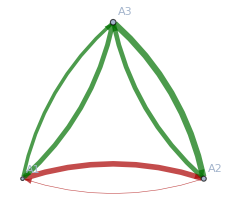

```mathematica
displayGraph[randomGameState,False]
```

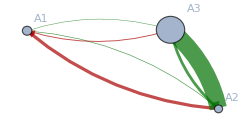

```mathematica
displayGraph[randomGameState,False,{Entity["City",{"Coventry","Coventry","UnitedKingdom"}],Entity["City",{"Sarajevo","FederacijaBosnaIHercegovina","BosniaHerzegovina"}],Entity["City",{"Berlin","Berlin","Germany"}]}]
```

#### Display line of play

Display a sequence of game states:

```mathematica
displayLineOfPlay[lineOfPlay_,showMetadataQ_] :=Map[Magnify[displayGraph[#,showMetadataQ],0.60]&,lineOfPlay]
```

#### Tactic plot

```mathematica
randomMatrixNear[IdentityMatrix[3]]
```

{{0.975839,-0.0145173,0.013843},{0.0173209,0.985098,-0.00779891},{-0.00684029,-0.00038488,0.978358}}

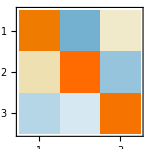

```mathematica
MatrixPlot[%]
```

## Experimentation

### Tests

#### Parameter Explorer

A widget for exploring parameter space for a simple scenario.  Moving the “redo” slider generates a new simulation without altering any of the other variables.  TODO: stop this from auto-updating continuously.

```mathematica
Manipulate[
Block[{},
α=alpha;
β=beta;
μ=mu;
δ=delta;
σ=sigma;
breadth=bre;
depth=dep;
probes = prob;
nearness=near;
discountVector = Table[δ^i,{i,0,depth-1}];

showLinesOfPlay[runFrame[newState[{1,1,1},{{0.8,0.2,0},{0.2,0.8,-0.1},{0,0,0.9}}]],False] // Column],

{{alpha,2.5,"α"},2,3},{{beta,1.1,"β"},1,10},{{mu,3,"μ"},1,10},{{delta,0.8,"δ"},0.001,1},{{sigma,0.01,"σ"},0.001,4},{{bre,15,"breadth"},1,25,1},{{dep,5,"depth"},1,15,1},{{prob,5,"probes"},1,15,1},{{near,0.05,"nearness"},0.001,1},{redo,0,1}]
```

#### WWI

Very preliminary: Europe (subset), August 1914.

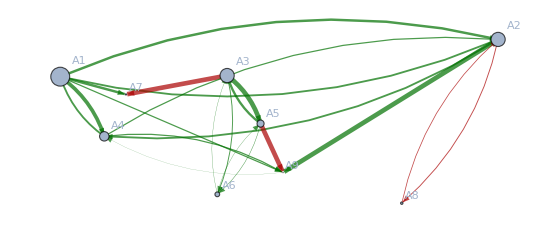

```mathematica
wwiCities = {Entity["City",{"Coventry","Coventry","UnitedKingdom"}],Entity["City",{"Moscow","Moscow","Russia"}],Entity["City",{"Berlin","Berlin","Germany"}],Entity["City",{"Bourges","Centre","France"}],Entity["City",{"Vienna","Vienna","Austria"}],Entity["City",{"Rome","Lazio","Italy"}],Entity["City",{"Brussels","Brussels","Belgium"}],Entity["City",{"Istanbul","Istanbul","Turkey"}],Entity["City",{"Sarajevo","FederacijaBosnaIHercegovina","BosniaHerzegovina"}]};wwiSizes = {0.8,0.6,0.6,0.4,0.3,0.2,0.05,0.1,0.02};
wwiTactics = {
{0.94,0.02,0,0.03,0,0,0,0,0},
{0.02,0.94,0,0.02,0,0,0,-0.05,0},
{0,0,0.90,0,0.05,0.01,0,0,0},
{0.03,0.02,0,0.98,0,0,0,0,0.05},
{0,0,0.05,0,0.94,0.01,0,0,0},
{0,0,0.01,0,0.01,1,0,0,0},
{0.02,0,-0.05,0,0,0,1,0,0},
{0,-0.01,0,0,0,0,0,0.95,0},
{0.01,0.05,0,0.02,-0.1,0,0,0,0.95}} ;
wwi = newState[wwiSizes,wwiTactics];
displayGraph[wwi,False,wwiCities]
```

```mathematica
wwiTactics// MatrixForm
```

(0.94 | 0.02 | 0 | 0.03 | 0 | 0 | 0 | 0 | 0
0.02 | 0.94 | 0 | 0.02 | 0 | 0 | 0 | -0.05 | 0
0 | 0 | 0.9 | 0 | 0.05 | 0.01 | 0 | 0 | 0
0.03 | 0.02 | 0 | 0.98 | 0 | 0 | 0 | 0 | 0.05
0 | 0 | 0.05 | 0 | 0.94 | 0.01 | 0 | 0 | 0
0 | 0 | 0.01 | 0 | 0.01 | 1 | 0 | 0 | 0
0.02 | 0 | -0.05 | 0 | 0 | 0 | 1 | 0 | 0
0 | -0.01 | 0 | 0 | 0 | 0 | 0 | 0.95 | 0
0.01 | 0.05 | 0 | 0.02 | -0.1 | 0 | 0 | 0 | 0.95)